```mathematica
q=E^(-Pi); (*Expansion coff*)
(**Phi field, t should be understood as Sqrt[λ]*ϕ*t in our paper**)
phit[n_]:=2Sqrt[2]Pi/EllipticK[1/2]((-1)^n q^(n+1/2))/(1+q^(2n+1))Sin[(2n+1)t];  (**Phi field**)
(**Time derivative of Phi field**)
phitt[n_]:=2Sqrt[2]Pi/EllipticK[1/2]((-1)^n q^(n+1/2))/(1+q^(2n+1))Cos[(2n+1)t]*(2n+1);
```

```mathematica
N[FourierCoefficient[phit[0]+phit[1]+phit[2],t,n]]
```

Piecewise[{{0.-0.477503 ⅈ, n==1.}, {0.+0.477503 ⅈ, n==-1.}, {0.-0.0215247 ⅈ, n==-3.}, {0.+0.0215247 ⅈ, n==3.}, {0.-0.000930244 ⅈ, n==5.}, {0.+0.000930244 ⅈ, n==-5.}, {0., True}}]

```mathematica
N[FourierCoefficient[(phitt[0]+phitt[1]+phitt[2])^2,t,n]]
```

Piecewise[{{0.00861177, n==-6.||n==6.}, {0.0000216338, n==-10.||n==10.}, {-0.000600698, n==-8.||n==8.}, {-0.0572268, n==-4.||n==4.}, {0.16574, n==-2.||n==2.}, {0.464401, n==0.}, {0., True}}]

```mathematica
N[FourierCoefficient[(phit[0]+phit[1]+phit[2])^4,t,n]]
```

Piecewise[{{-6.93088×10^-11, n==-18.||n==18.}, {3.94312×10^-9, n==-16.||n==16.}, {7.48836×10^-13, n==-20.||n==20.}, {-1.45376×10^-7, n==-14.||n==14.}, {3.97493×10^-6, n==-12.||n==12.}, {0.00116898, n==-8.||n==8.}, {-0.237919, n==-2.||n==2.}, {-0.000078676, n==-10.||n==10.}, {-0.0119178, n==-6.||n==6.}, {0.0820766, n==-4.||n==4.}, {0.333333, n==0.}, {0., True}}]

```mathematica
Plot[{(phit[0]+phit[1]+phit[2])^4,phitt[0]^2,phit[0]},{t,-Pi,Pi}]
```

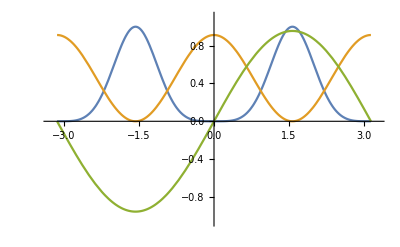

```mathematica
N[Integrate[1/(2Pi) phit[0]^4E^(-I t),{t,0,2Pi}]]
```

0.

```mathematica
N[Integrate[1/(2Pi) phit[0]^4E^(-I 2t),{t,-Pi,Pi}]]
```

-0.207953

```mathematica
FourierCoefficient[JacobiSN[t,i]^4,t,5]
```

FourierCoefficient[JacobiSN[t,i]^4,t,5]

```mathematica
FourierCoefficient[JacobiSN[t,-1]^4,t,5]
```

FourierCoefficient[JacobiSN[t,-1]^4,t,5]